## Images

x | y | fx | fy
50. | 1. | 1 | 1
54.789 | 14.121 | 0.0584058 | 0.353042
54.2671 | 12.6756 | 0.0227975 | 0.141721
56.0322 | 10.5546 | 0.00851942 | 0.0558006
60.6215 | 7.66995 | 0.00314236 | 0.0213464
66.2276 | 4.45039 | 0.0012233 | 0.00761365
70.1934 | 1.86954 | 0.000412774 | 0.00209785
71.6872 | 0.714 | 0.0000615384 | 0.000270094
71.8931 | 0.536726 | 1.32855×10^-6 | 5.55492×10^-6
71.8973 | 0.533041 | 5.74076×10^-10 | 2.38742×10^-9
71.8973 | 0.53304 | 1.00614×10^-16 | 4.51028×10^-16
71.8973 | 0.53304 | -1.38778×10^-17 | 0.

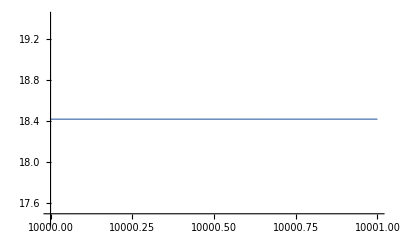
```mathematica
p1=-Graphics-
```

-Graphics-

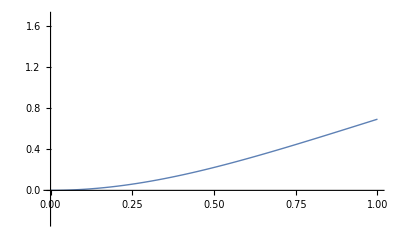
```mathematica
p2=-Graphics-
```

-Graphics-

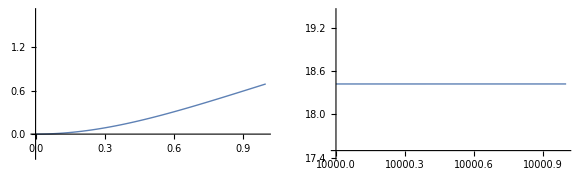

```mathematica
GraphicsGrid[{{p2,p1}}]
```

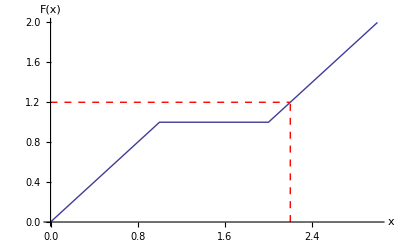

```mathematica
a={2.2,0};f[x_]:=If[x<1,x,If[x<2,1,x-1]];
p1=Show[Plot[f[x],{x,0,3},AxesLabel->{"x","F(x)"},PlotRange->{0,2}],ParametricPlot[{a[[1]],t},{t,0,If[Abs[f[a[[1]]]]>0,f[a[[1]]],.001]},PlotStyle->{Dashed,Red}],ParametricPlot[{t,f[a[[1]]]},{t,0,If[Abs[a[[1]]]>0,a[[1]],.001]},PlotStyle->{Dashed,Red}]]
```

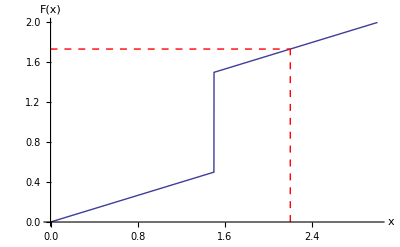

```mathematica
a={2.2,0};f[x_]:=If[x≤  1.5,1/3x,1/3(x+3)];
p2=Show[Plot[f[x],{x,0,3},AxesLabel->{"x","F(x)"},PlotRange->{0,2}],ParametricPlot[{a[[1]],t},{t,0,If[Abs[f[a[[1]]]]>0,f[a[[1]]],.001]},PlotStyle->{Dashed,Red}],ParametricPlot[{t,f[a[[1]]]},{t,0,If[Abs[a[[1]]]>0,a[[1]],.001]},PlotStyle->{Dashed,Red}]]
```

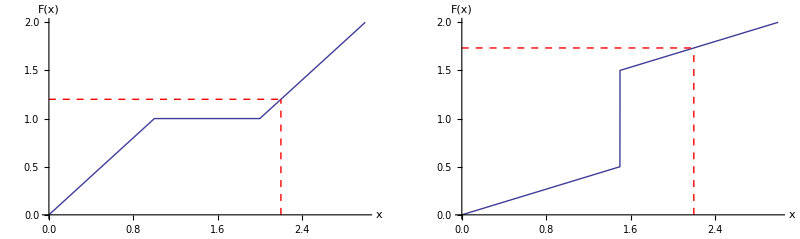

```mathematica
GraphicsGrid[{{p1,p2}}]
```

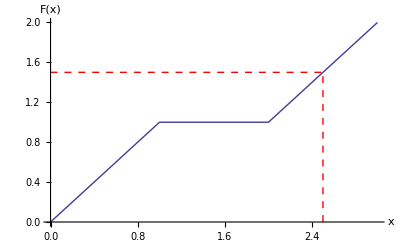

```mathematica
f[x_]:=If[x<1,x,If[x<2,1,x-1]];
g[y_]:=If[y>1,y+1,If[y<1,y,2]];
a={0,1.5};
r1=Show[Plot[f[x],{x,0,3},AxesLabel->{"x","F(x)"},PlotRange->{0,2}],ParametricPlot[{t,a[[2]]},{t,0,g[a[[2]]]},PlotStyle->{Dashed,Red}],ParametricPlot[{g[a[[2]]],t},{t,0,a[[2]]},PlotStyle->{Dashed,Red}]]
```

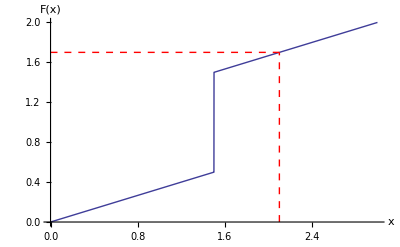

```mathematica
f[x_]:=If[x≤  1.5,1/3x,1/3(x+3)];
g[y_]:=If[y>1.5,3 y-3,If[y>.5,1.5,3 y]];
a={0,1.7};
r2=Show[Plot[f[x],{x,0,3},AxesLabel->{"x","F(x)"},PlotRange->{0,2}],ParametricPlot[{t,a[[2]]},{t,0,g[a[[2]]]},PlotStyle->{Dashed,Red}],ParametricPlot[{g[a[[2]]],t},{t,0,a[[2]]},PlotStyle->{Dashed,Red}]]
```

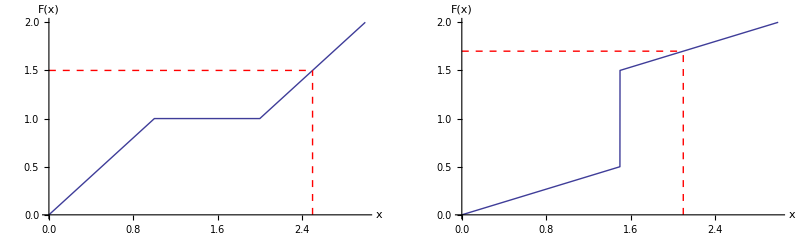

```mathematica
GraphicsGrid[{{r1,r2}}]
```

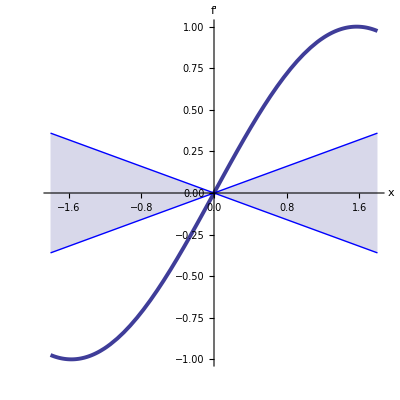

```mathematica
Show[Plot[Sin[x],{x,-1.8,1.8},PlotStyle->{Thickness[.007]},AspectRatio->1,AxesLabel->{Style["x",Large],Style["f'",Large]}],Plot[0,{x,-1.8,1.8},AspectRatio->1,Axes->False,PlotStyle->{Opacity[.0001]}],Plot[{-.2 (x)+Sin[0],.2( x)+Sin[0]},{x,-1.8,1.8},Filling->{1->{2}},AspectRatio->1,Axes->False,PlotStyle->{Blue,Blue}]]
```

## Tracking the gradient during Newton’s method

### The monthly payment objective function

```mathematica
f[x_,y_]:=(30-y)(1+10^9/((108-x)^2(30-y)^5))^(x/12)/x ;
```

### The initial guess

```mathematica
{xbar,ybar}={50.0,1.0};
list={{xbar,ybar,1,1}};
```

### Defining the various partial derivative functions.

```mathematica
fx[x_,y_]=D[f[x,y], x];
fxx[x_,y_]=D[f[x,y], x,x];
fxy[x_,y_]=D[f[x,y], x,y];
fy[x_,y_]=D[f[x,y], y];
fyy[x_,y_]=D[f[x,y], y,y];
fyx[x_,y_]=D[f[x,y], y,x];
```

### Solving the Newton equations corresponding to the stationary point equations for the objective function (enter repeatedly to swap old guesses with new)

```mathematica
sol=Solve[{fx[xbar,ybar]+fxx[xbar,ybar](x-xbar)+fxy[xbar,ybar](y-ybar)==0,fy[xbar,ybar]+fyx[xbar,ybar](x-xbar)+fyy[xbar,ybar](y-ybar)==0},{x,y}];
xbar=x/.sol[[1]];ybar=y/.sol[[1]];
list=Append[list,{x/.sol[[1]],y/.sol[[1]],fx[x/.sol[[1]],y/.sol[[1]]],fy[x/.sol[[1]],y/.sol[[1]]]}];
TableForm[Prepend[list,{Text[x],Text[y],Text[fx],Text[fy]}]]
```

Newton’s optimization method generates these guesses:

x | y | fx | fy
50. | 1. | 1 | 1
54.789 | 14.121 | 0.0584058 | 0.353042
54.2671 | 12.6756 | 0.0227975 | 0.141721
56.0322 | 10.5546 | 0.00851942 | 0.0558006
60.6215 | 7.66995 | 0.00314236 | 0.0213464
66.2276 | 4.45039 | 0.0012233 | 0.00761365
70.1934 | 1.86954 | 0.000412774 | 0.00209785
71.6872 | 0.714 | 0.0000615384 | 0.000270094
71.8931 | 0.536726 | 1.32855×10^-6 | 5.55492×10^-6
71.8973 | 0.533041 | 5.74076×10^-10 | 2.38742×10^-9
71.8973 | 0.53304 | 1.00614×10^-16 | 4.51028×10^-16
71.8973 | 0.53304 | -1.38778×10^-17 | 0.

## Nearly stationary not near stationary point

```mathematica
Manipulate[Plot[Log[x^2+1],{x,a,a+1},PlotStyle->{Thick},PlotRange->{Log[(a+1)^2+1]-1,Log[(a+1)^2+1]+1}],{{a,10000},0,10000,10}]
```

## Continuity and Reverse Continuity

### Continuity

#### Continuous

```mathematica
Manipulate[Show[Plot[f[x],{x,0,3},AxesLabel->{"x","F(x)"},PlotRange->{0,2}],ParametricPlot[{a[[1]],t},{t,0,If[Abs[f[a[[1]]]]>0,f[a[[1]]],.001]},PlotStyle->{Dashed,Red}],ParametricPlot[{t,f[a[[1]]]},{t,0,If[Abs[a[[1]]]>0,a[[1]],.001]},PlotStyle->{Dashed,Red}]],{{a,{1.5,0}},{0,0},{3,0},Locator},Initialization:>(f[x_]:=If[x<1,x,If[x<2,1,x-1]];)]
```

#### Not continuous

```mathematica
Manipulate[Show[Plot[f2[x],{x,0,3},AxesLabel->{"x","F(x)"},PlotRange->{0,2}],ParametricPlot[{a[[1]],t},{t,0,If[Abs[f2[a[[1]]]]>0,f2[a[[1]]],.001]},PlotStyle->{Dashed,Red}],ParametricPlot[{t,f2[a[[1]]]},{t,0,If[Abs[a[[1]]]>0,a[[1]],.001]},PlotStyle->{Dashed,Red}]],{{a,{1.5,0}},{0,0},{3,0},Locator},Initialization:>(f2[x_]:=If[x≤  1.5,1/3x,1/3(x+3)];)]
```

### Reverse Continuity

#### Not reverse continuous

```mathematica
Manipulate[Show[Plot[f3[x],{x,0,3},AxesLabel->{"x","F(x)"},PlotRange->{0,2}],ParametricPlot[{t,a[[2]]},{t,0,g3[a[[2]]]},PlotStyle->{Dashed,Red}],ParametricPlot[{g3[a[[2]]],t},{t,0,a[[2]]},PlotStyle->{Dashed,Red}]],{{a,{0,1.5}},{0,0},{0,2},Locator},Initialization:>(f3[x_]=If[x<1,x,If[x<2,1,x-1]];g3[y_]=If[y>1,y+1,If[y<1,y,2]];)]
```

#### Reverse continuous

```mathematica
Manipulate[Show[Plot[f4[x],{x,0,3},AxesLabel->{"x","F(x)"},PlotRange->{0,2}],ParametricPlot[{t,a[[2]]},{t,0,g4[a[[2]]]},PlotStyle->{Dashed,Red}],ParametricPlot[{g4[a[[2]]],t},{t,0,a[[2]]},PlotStyle->{Dashed,Red}]],{{a,{0,1.5}},{0,0},{0,2},Locator},Initialization:>(f4[x_]=If[x≤  1.5,1/3x,1/3(x+3)];
g4[y_]=If[y>1.5,3 y-3,If[y>.5,1.5,3 y]];)]
```

## Animated bow-tie

```mathematica
Manipulate[Show[Plot[Sin[x],{x,-1.8,1.8},PlotStyle->{Thickness[.007]},AspectRatio->1,AxesLabel->{Style["x",Large],Style["f'",Large]}],Plot[{-L (x-center)+Sin[center],L( x-center)+Sin[center]},{x,center-miniaturize,center+miniaturize},Filling->{1->{2}},AspectRatio->1,Axes->False,PlotStyle->{Blue,Blue}]],{{center,0,"x̄"},-1.8,1.8},{{L,.2},0,1},{{miniaturize,1.8},0.0000001,1.8}]
```

## A look at f’(x) for the first example above

```mathematica
f[x_]:=Log[x^2+1]
```

```mathematica
df[x_]=D[f[x],x]
```

(2 x)/(1+x^2)

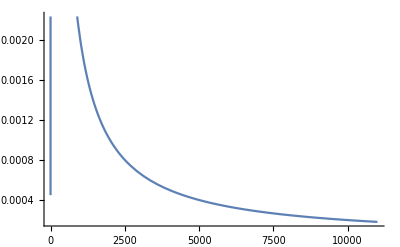

```mathematica
Plot[df[x],{x,0,11000}]
```

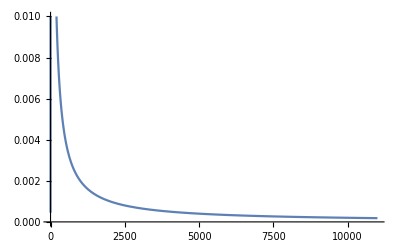

```mathematica
Plot[df[x],{x,0,11000},PlotRange->{0,.01}]
```

### Computing f’’(x) for the first example above

```mathematica
f[x_]:=Log[x^2+1]
```

```mathematica
df[x_]=D[f[x],x];
d2f[x_]=D[df[x],x]
```

-(4 x^2)/((1+x^2)^2)+2/(1+x^2)

```mathematica
Abs[d2f[100000]]//N
```

2.×10^-10

A nearly zero scaling factor!